```mathematica
Remove["Global`*"]
(*Jim's Weighting Funtions*)
w[t_]:=a+b Cos[π t]
f[t_]:=Piecewise[{{w[t], Abs[t]≤1}, {0, True}}]
FourierTransform[f[t],t,ω]

F[ω_,a_,b_]=%;
Limit[F[ω,a,b],ω->0]
F[ω_,a_,b_]=F[ω,a,b]/Limit[F[ω,a,b],ω->0] //FullSimplify
```

(b Sin[ω])/(√(2 π) (π-ω))+(a √(2/π) Sin[ω])/ω-(b Sin[ω])/(√(2 π) (π+ω))

a √(2/π)

(a π^2 Sin[ω]-a ω^2 Sin[ω]+b ω^2 Sin[ω])/(a π^2 ω-a ω^3)

Hanning Window

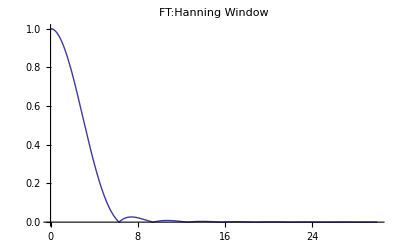

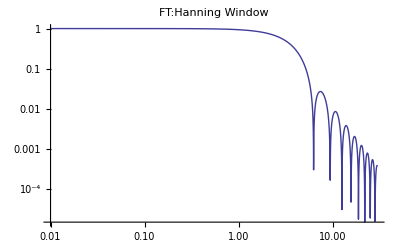

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ω→7.42023}

0.0267076

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{6.58646,8.58818}

2.00172

Hamming Window

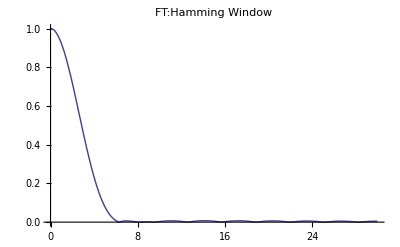

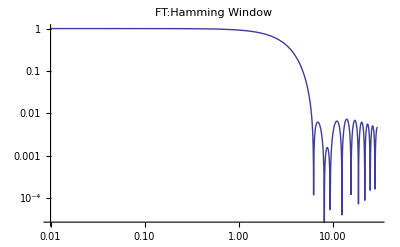

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ω→6.95191}

0.00628352

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{6.45936,7.65216}

1.1928

```mathematica
Print["Hanning Window"]
Plot[Abs[F[ω,.5,.5]],{ω,0,30},PlotRange->All,PlotLabel->"FT:Hanning Window"]
LogLogPlot[Abs[F[ω,.5,.5]],{ω,0.01,30},PlotRange->All,PlotLabel->"FT:Hanning Window"]
solnhan=Solve[{D[F[ω,.5,.5],ω]==0,1<ω<10},ω][[1]]
Abs[F[ω,.5,.5]]/.solnhan
fw=ω/.Solve[{F[ω,.5,.5]==F[ω/.solnhan,.5,.5]/2,6<ω<9},ω]
fw[[2]]-fw[[1]]
Print["Hamming Window"]
Plot[Abs[F[ω,.54,.46]],{ω,0,30},PlotRange->All,PlotLabel->"FT:Hamming Window"]
LogLogPlot[Abs[F[ω,.54,.46]],{ω,0.01,30},PlotRange->All,PlotLabel->"FT:Hamming Window"]
solham=Solve[{D[F[ω,.54,.46],ω]==0,1<ω<10},ω][[1]]
Abs[F[ω,.54,.46]]/.solham
fw=ω/.Solve[{F[ω,.54,.46]==F[ω/.solham,.54,.46]/2,6<ω<8},ω]
fw[[2]]-fw[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

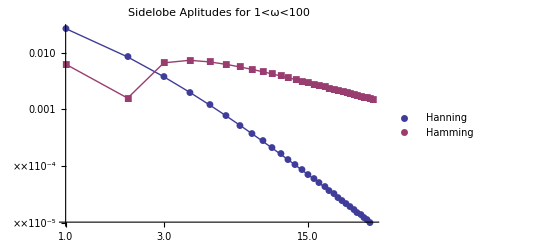

```mathematica
ListLogLogPlot[{Abs[F[ω/.Solve[{D[F[ω,.5,.5],ω]==0,1<ω<100},ω],.5,.5]],Abs[F[ω/.Solve[{D[F[ω,.54,.46],ω]==0,1<ω<100},ω],.54,.46]]},PlotRange->All,PlotLegends->{"Hanning","Hamming"},Joined->True,PlotMarkers->Automatic,PlotLabel->"Sidelobe Aplitudes for 1<ω<100"]
```